# Nonlinear analysis of a fold

Alison Ord

## Background

Are folded rocks a snapshot of a nonlinear dynamic system?
  
  I have already used the Wolfram Language for some of these analyses, but I wish to use the Wolfram Language for all of these analyses, and interactively with the data and themselves so there may be feedback between the different forms of analysis providing an optimal nonlinear description of the data.
  
  Putting all this together I think is new, but the most important aspect is providing an easy to use tool from the nonlinear dynamical toolbox for geologists to explore their data in a completely new way.
  
  The use of the tool requires a pedagogic approach to its development. Some prioritisation will be required! Also, I have much data from other sources, 1 D, 2 D and 3 D, hyperspectral analyses, mechanical computational simulations created in external software, requiring this approach.
  
  Note that I already have issues just in the formatting.

## The Problem

When layered rocks are shortened during tectonic events, the most obvious structures formed are folds. Folding of layered rocks causes a change in geological structure that can lead to a fundamental modification of the mechanical and hydraulic properties of the rock mass across several orders of magnitude in length - typically from the millimetre to the kilometre-scale. 

  The understanding of how, why and on which scale folding occurs therefore has fundamental implications for problems in geology and engineering, including prediction of the form and location of hydrocarbon accumulations [1], salt domes [2], groundwater flow [3], mineralization [4, 5], and rock slope stability [6, 7, 8].

We have prepared three dimensional models of natural fold systems using photogrammetry and we explore the multifractal geometry using the Wavelet Transform Modulus Maxima (WTMM) method[30-34] and recurrence quantification[29,35-37] in order to delineate the dynamics of naturally folded systems.We show for comparison numerical results of quasiperiodic signals and Hénon mappings.The property of interest with the Hénon low two-dimensional mapping, as well as its mechanical underpinning, is its possession of a strange attractor, of interest to geology and naturally occurring fold systems since it was suggested they may display spatial chaos in their geometry [8, 38]. The Lorenz model and its strange attractor, the basis for weather exploration, is associated with three- or higher dimensional dynamical systems [27].

## The Data

### Surfaces of folded rocks

First we see a multiply deformed rock with porphyroblasts from Rum Jungle in Australia.

```mathematica
SetDirectory["C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\RumJungle images"]
```

C:\Users\Alison\Documents\Personal\Wolfram Summer School\Projects\RumJungle images

```mathematica
image=Import["20171001-199A8116.jpg"];
```

```mathematica
imageshow=ImageResize[image,Medium]
```

-Graphics-

It is then photographed from multiple angles, and the images collated and analysed within CloudCompare. This image shows interpreted cloud of points, with a single line through the points denoting the data collected, and shown in cross section in the following figure.

```mathematica
image=Import["Ord_C_profile_3.jpg"];
```

```mathematica
imageshow=ImageResize[image,Medium]
```

-Graphics-

Not all rocks, even, or especially, folded rocks. Here is another multiply folded rock, this time from Broken Hill in Australia. First, we look at the rock, sitting on a structured page used for collating (wrong word) the photographic images.

```mathematica
SetDirectory["C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\BHill images"]
```

C:\Users\Alison\Documents\Personal\Wolfram Summer School\Projects\BHill images

```mathematica
image=Import["20171001-199A8030.jpg"];
```

```mathematica
imageshow=ImageResize[image,Medium]
```

-Graphics-

Second, we see the cloud of points for that system, derived from the photo collection.

```mathematica
image=Import["Ord_samp_1.jpg"];
```

```mathematica
imageshow=ImageResize[image,Medium]
```

-Graphics-

Third, we have the cloud of points just of the rock, followed by sections through the rock cloud, viewed from different orientations.

How do I size the images? place them? for example, three images of sections in a row?

```mathematica
image=Import["sections.jpg"];
```

```mathematica
imageshow=ImageResize[image,Medium]
```

-Graphics-

```mathematica
image=Import["sections2.jpg"];
```

```mathematica
imageshow=ImageResize[image,Medium]
```

-Graphics-

```mathematica
image=Import["sections5.jpg"];
```

```mathematica
imageshow=ImageResize[image,Medium]
```

-Graphics-

```mathematica
image=Import["sections4.jpg"];
```

```mathematica
imageshow=ImageResize[image,Medium]
```

-Graphics-

We now export (x,y) coordinates for the chosen section.

import x and y values directly from the excel spreadsheet and plot the cross section

### Drill core

```mathematica
import pictures of core
```

core import of pictures

1D

Hyperspectral analyses
	Density
	Magnetic Susceptibility

3D

```mathematica
Element  abundance
```

abundance Element

## The Analyses

### Spatial attractors

```mathematica
SetDirectory["C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\BHill images"]
```

C:\Users\Alison\Documents\Personal\Wolfram Summer School\Projects\BHill images

```mathematica
Needs["JLink`"]
ReinstallJava[JVMArguments -> "-Xmx8192m"];
```

Here we show the spatial attractor for the data with a lag of 20, in various styles.

```mathematica
m=Import["Section contour #4 lag 1.xlsx",{"Sheets",3}];
```

```mathematica
ListPointPlot3D[m]
```

-Graphics3D-

```mathematica
ListPointPlot3D[m,DataRange->Automatic,ColorFunctionScaling->True,ColorFunction->"Rainbow",Axes->True,PlotRange->All,BoxRatios->{1,1,1},AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
junk=BSplineCurve[{m}];
```

```mathematica
Tube[junk];
```

```mathematica
Graphics3D[{Orange,Specularity[White,10],Tube[junk,.002]},Axes->True,PlotRange->All,Boxed->True,BoxRatios->{1, 1, 1},BoxStyle->Directive[Dashed,Gray],Background->Black,LabelStyle->Directive[Black,Bold],AxesLabel->{t, t+5, t+10},ViewPoint->Front,ImagePadding->5]
```

-Graphics3D-

```mathematica
Graphics3D[{Yellow,Specularity[White,10],Tube[junk,.003]},Axes->True,PlotRange->All,Boxed->True,BoxRatios->{1, 1, 1},BoxStyle->Directive[Dashed,Gray],Background->Black,LabelStyle->Directive[Black,Bold],AxesLabel->{i, i+20, i+40},ViewPoint->Above,PreserveImageOptions->True,ImagePadding->5]
```

-Graphics3D-

```mathematica
Graphics3D[{Orange,Specularity[White,10],Tube[junk,.002]},Axes->True,PlotRange->All,Boxed->True,BoxRatios->{1, 1, 1},BoxStyle->Directive[Dashed,Gray],Background->Black,LabelStyle->Directive[Black,Bold],AxesLabel->{i, i+20,i+40},ViewPoint->{-2,2,0},ImagePadding->4]
```

-Graphics3D-

### Wavelet transforms

```mathematica
SetDirectory["C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\BHill images"]
```

C:\Users\Alison\Documents\Personal\Wolfram Summer School\Projects\BHill images

```mathematica
data=ReadList["rock4z"];
```

```mathematica
datalist=Flatten[data];
```

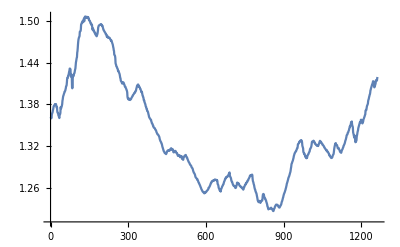

```mathematica
ListPlot[datalist,PlotRange->All,Joined->True]
```

```mathematica
ListPlot[datalist];
```

```mathematica
ListPlot[Accumulate[datalist]];
```

```mathematica
Accumulate[datalist][[-1]]
```

1689.82

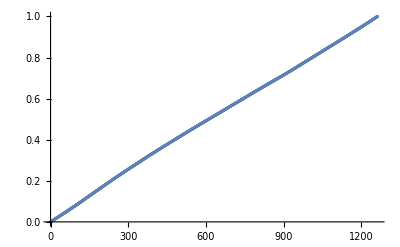

```mathematica
ListPlot[Accumulate[datalist/%],GridLines->None]
```

```mathematica
cwd=ContinuousWaveletTransform[datalist,WaveletScale->1]
```

ContinuousWaveletData[…]

```mathematica
cwd[All,"Values"];
```

```mathematica
recwd=Re[%];
```

```mathematica
cwd[{"WaveletScale","Octaves","Voices"}]
```

{1,9,4}

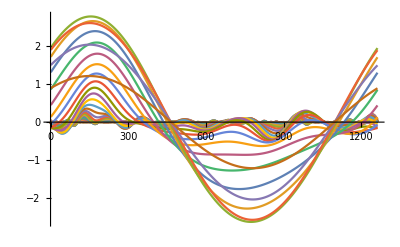

```mathematica
ListLinePlot[recwd,PlotRange->All]
```

```mathematica
cwd["Wavelet"]
```

MexicanHatWavelet[1]

```mathematica
{cwd["Scales"],cwd["WaveletScale"],cwd["WaveletIndex"]}
```

{{{1,1}→1.18921,{1,2}→1.41421,{1,3}→1.68179,{1,4}→2.,{2,1}→2.37841,{2,2}→2.82843,{2,3}→3.36359,{2,4}→4.,{3,1}→4.75683,{3,2}→5.65685,{3,3}→6.72717,{3,4}→8.,{4,1}→9.51366,{4,2}→11.3137,{4,3}→13.4543,{4,4}→16.,{5,1}→19.0273,{5,2}→22.6274,{5,3}→26.9087,{5,4}→32.,{6,1}→38.0546,{6,2}→45.2548,{6,3}→53.8174,{6,4}→64.,{7,1}→76.1093,{7,2}→90.5097,{7,3}→107.635,{7,4}→128.,{8,1}→152.219,{8,2}→181.019,{8,3}→215.269,{8,4}→256.,{9,1}→304.437,{9,2}→362.039,{9,3}→430.539,{9,4}→512.},1,{{1,1},{1,2},{1,3},{1,4},{2,1},{2,2},{2,3},{2,4},{3,1},{3,2},{3,3},{3,4},{4,1},{4,2},{4,3},{4,4},{5,1},{5,2},{5,3},{5,4},{6,1},{6,2},{6,3},{6,4},{7,1},{7,2},{7,3},{7,4},{8,1},{8,2},{8,3},{8,4},{9,1},{9,2},{9,3},{9,4}}}

```mathematica
{cwd["LogScalogramFunction"],cwd["LinearScalogramFunction"]}
```

{InterpolatingFunction[{{1., 1262.}, {0.25, 9.}}, <>],InterpolatingFunction[{{1., 1262.}, {1.18921, 512.}}, <>]}

```mathematica
WaveletScalogram[cwd,ColorFunction->"CherryTones",Ticks->Full]
```

-Graphics-

```mathematica
cf[x_]:=Blend[{RGBColor[0.,0.,0.3],RGBColor[0.,0.,0.5],RGBColor[0,0.1,0.5],RGBColor[0,0.2,1],RGBColor[0,0.5,1],RGBColor[0.2,0.7,1],RGBColor[0.5,0.8,1],RGBColor[0.5,.9,.9],RGBColor[0.5,1.,0.9],RGBColor[0.7,1,0.7],RGBColor[0.8,1,0.5],RGBColor[1,1,0],RGBColor[1,0.8,0],RGBColor[1,0.5,0],RGBColor[1,.25,0],RGBColor[1,.1,0.],RGBColor[1,.0,0.],RGBColor[.9,.0,0.],RGBColor[0.8,0.,0.],RGBColor[0.5,0.,0.],RGBColor[.25,0.,0.],RGBColor[0.1,0,0]},x];
```

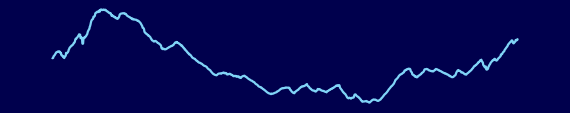
-Graphics-
-Graphics-

```mathematica
Column[{ListLinePlot[datalist,Axes->None,ImageSize->570,AspectRatio->0.2,PlotRangePadding->None,PlotRange->All,Background->cf[0],PlotStyle->cf[0.3]],WaveletScalogram[cwd,ColorFunction->(cf[#]&),Axes->True,ImageSize->570,PlotRangePadding->None,Ticks->Full]},Spacings->0.2]
```

```mathematica
ListPlot3D[recwd,ColorFunction->"DarkRainbow",AxesLabel->{"depth","scale"},Mesh->None,PlotRange->All]
```

-Graphics3D-

Visualise a stationary wavelet transform using a common x axis plot . Mathematica featured example

```mathematica
dwd=StationaryWaveletTransform[datalist,Automatic,8];
```

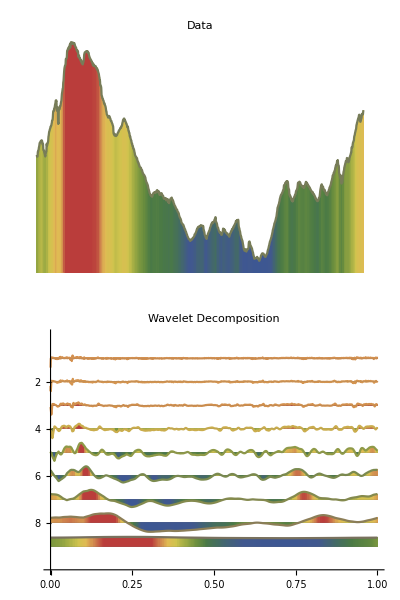

```mathematica
Column[{ListLinePlot[datalist,ImageSize->570,AspectRatio->0.2,Axes->None,ColorFunction->"DarkRainbow",Filling->Axis,PlotLabel->Style["Data",FontFamily->"Verdana",Brown,Bold,16],InterpolationOrder->2],WaveletListPlot[dwd,DataRange->{0,1},ColorFunction->"DarkRainbow",Filling->Axis,ImageSize->570,PlotRangePadding->None,TicksStyle->Directive[13,FontFamily->"Verdana"],PlotLabel->Style["Wavelet Decomposition",FontFamily->"Verdana",Brown,Bold,16]]}]
```

Visualise a stationary wavelet transform using a common y axis plot . Mathematica featured example

```mathematica
dwd=StationaryWaveletTransform[datalist,Automatic,8];
```

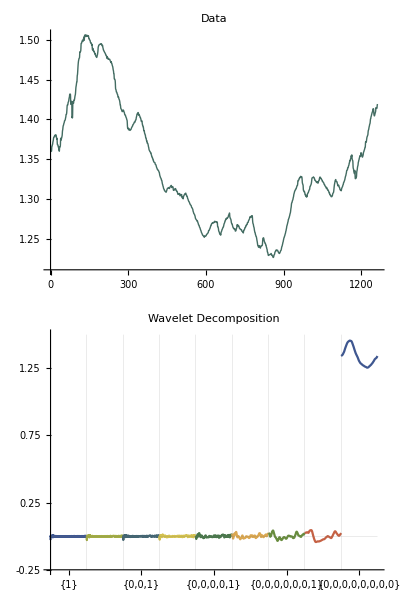

```mathematica
Column[{ListLinePlot[data,ImageSize->570,AspectRatio->0.2,PlotStyle->Directive[Thick,ColorData["DarkRainbow",0.2]],Axes->{False,True},TicksStyle->Directive[13,FontFamily->"Verdana"],PlotLabel->Style["Data",FontFamily->"Verdana",Brown,Bold,16],InterpolationOrder->2,ImagePadding->{{20,Automatic},{Automatic,Automatic}}],WaveletListPlot[dwd,Automatic,PlotStyle->(ColorData["DarkRainbow"]/@Riffle[#,#2]&@@Partition[Range[0.05,0.85,0.8/7],4]),ImageSize->570,PlotLayout->"CommonYAxis",Ticks->Full,TicksStyle->Directive[13,FontFamily->"Verdana"],PlotLabel->Style["Wavelet Decomposition",FontFamily->"Verdana",Brown,Bold,16],ImagePadding->{{30,Automatic},{Automatic,Automatic}}]},Alignment->Right]
```

### Singularity spectra

### Hurst exponents

#### Include mtca code

### Recurrence plots

### Fourier transforms

### Recurrence histograms

### Networks

#### Include mtca code

### Discovery of physics from data

### The vision is of moving a cursor through (x, y, z) coordinates for the surface of a deformed, folded rock and to watch data driven analyses change in different windows including : spatial attractors, wavelet transforms, singularity spectra, Hurst exponents, recurrence plots (including the ability for cross - and joint - recurrence plots and their quantitative analysis), Fourier transforms, recurrence histograms, networks, and sparsely determined nonlinear determinations of the differential equations describing the data.

This isn’t going to work now as the cloud of points exists only in CloudCompare. It should be easier to consider windows moving up and down drill core data.

#### References Brunton et al. da Silva, Higdon, Brunton and Kutz 2019 Discovery of physics from data Ord et al. JSG Ord et al. PhilTrans Ord 1994 Bacry Arneodo et al.